```mathematica
ClearAll["Global`*"]
```

# CSC Matrix Tester

## Generate rect CSC matrix in CATSPDEs sparse format

### Set input data

```mathematica
rows=10; (* numb of rows *)
cols=6; (* ″ cols *)
sparsity=.6; (* % of zero elements *)
```

### Compute sparse matrix A and vectors u, v for multiplications by A.u, A^T.v

```mathematica
nnzeros=Round[(1-sparsity) rows cols];
coords=Table[{RandomInteger@{1,rows},RandomInteger@{1,cols}}-> RandomInteger@{1,20},{i,nnzeros}];
A=SparseArray[coords,{rows,cols}];
```

```mathematica
u=Table[RandomInteger@{1,20},{i,cols}]; 
v=Table[RandomInteger@{1,20},{i,rows}];
```

```mathematica
A//MatrixForm
```

```mathematica
mval={};
iptr={};
jptr={0};
Do[
k=jptr[[j]];
Do[
If[
A[[i,j]]≠0,
++k;
AppendTo[mval,A[[i,j]]];
AppendTo[iptr,i-1]
],{i,rows}];
AppendTo[jptr,k],{j,cols}]
```

### Export data

```mathematica
SetDirectory[NotebookDirectory[]<>"output/CSC"];
```

```mathematica
Export["A.dat",{
{rows,cols,jptr[[-1]]},
jptr,
iptr,
mval
}];
```

```mathematica
Export["u.dat",u];
Export["v.dat",v];
```

```mathematica
SetDirectory[NotebookDirectory[]<>"../HarwellBoeing"];
```

```mathematica
Export["mathematica.rra",A,"HarwellBoeing"];
```

### Check multiplication results

Output vectors should be zeros!

```mathematica
SetDirectory[NotebookDirectory[]<>"../output/CSC"];
```

```mathematica
AxU=Import["AxU.dat","List","LineSeparators"->{" "},"IgnoreEmptyLines"->True];
MatrixForm[AxU-A.u]
```

(0.
0.
0.
0.
0.
0.
0.
0.
0.
0.)

```mathematica
AxV=Import["AxV.dat","List","LineSeparators"->{" "},"IgnoreEmptyLines"->True];
MatrixForm[AxV-Transpose@A.v]
```

(0.
0.
0.
0.
0.
0.)

## Harwell–Boeing

```mathematica
matrixName="illc1033.rra"; (* mathematica.rra, illc1033.rra, e40r5000.rua, qc2534.cua *)
```

### Load from original HB–collection

```mathematica
SetDirectory[NotebookDirectory[]<>"../HarwellBoeing"];
```

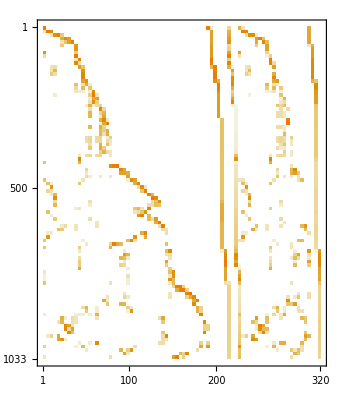

```mathematica
M=Import[matrixName];
MatrixPlot@M
```

### Load from CATSPDEs output

```mathematica
SetDirectory[NotebookDirectory[]<>"../output/CSC/HarwellBoeing"];
```

```mathematica
P=Import[matrixName];
MatrixPlot@P
```

-Graphics-

### Compare results

```mathematica
M[[1,1]]
P[[1,1]]
```

0.188982

0.188982

```mathematica
MatrixPlot[M-P]
```

-Graphics-